# Reálný trám

## dubový trám bez závaží

```mathematica
ClearAll["Global`*"]
Needs["NDSolve`FEM`"]
```

WolframAlphaQueryResults

scientific name | Quercus
material class | hardwood

```mathematica
(*zjistění potřebných parametrů*)
dens=650;
BeamLength= 10; 
BeamWidth = 0.25;
q=BeamWidth^2*dens*9.81;(*q=S*g*Rho=a^2*Rho*g*)
EE:= 11*10^9;
Izz=dens*BeamLength*BeamWidth^4/6;(*wikipedia->Izz=1/12*m*(sirka^2+vyska^2)*)
LoadDensity[X_]:=q
```

```mathematica
(*nyní řešíme dif. rci.*)
EulerBernoulliSolution = 
DSolve[
{
D[EE*Izz*D[y[X], X, X], X, X] == LoadDensity[X], 
y[-BeamLength/2]==0, 
y[BeamLength/2]==0, 
y'[-BeamLength/2]==0, 
y'[BeamLength/2]==0
}, 
y, 
X]
```

{{y→Function[{X},2.22955×10^-7-1.32349×10^-23 X-1.78364×10^-8 X^2+6.35275×10^-25 X^3+3.56727×10^-10 X^4]}}

```mathematica
(*nyní přichází na řadu přepis z úseček na trám (tedy vykradení notebooku pana Průši)*)
```

```mathematica
DisplacementEulerBernoulli[X_, Y_]:= {-Y*Sin[ArcTan[y'[X]]],y[X] + Y*(Cos[ArcTan[y'[X]]]-1)  }  /. EulerBernoulliSolution
u=Function[{X,Y},DisplacementEulerBernoulli[X, Y][[1]][[1]]]; 
v=Function[{X,Y},DisplacementEulerBernoulli[X, Y][[1]][[2]]]; 
BeamMesh = ToElementMesh[Rectangle[{-BeamLength/2, -BeamWidth/2}, {BeamLength/2, BeamWidth/2}]];
uif=ElementMeshInterpolation[{BeamMesh},u@@@BeamMesh["Coordinates"]]; 
vif=ElementMeshInterpolation[{BeamMesh},v@@@BeamMesh["Coordinates"]];
BeamMeshDeformed = ElementMeshDeformation[BeamMesh,{uif,vif}, "ScalingFactor"->10]["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]]; 
BeamMeshDeformed = ElementMeshDeformation[BeamMesh,{uif,vif}, "ScalingFactor"->10]["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]];
```

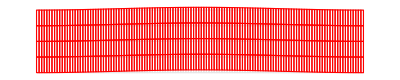

```mathematica
(*nyní jen vykreslíme*)
Show[BeamMesh["Wireframe"], ImageSize->Full];
Show[BeamMeshDeformed, ImageSize->Full];
Show[
BeamMesh["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[GrayLevel[0.9]],FaceForm[]]]],
ElementMeshDeformation[BeamMesh,{uif,vif}, "ScalingFactor"->10]["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]],
ImageSize->Full]
```

## Dubový trám se závažím

```mathematica
(*jediná věc co se změní bude parametr q*)
ClearAll["Global`*"]
Needs["NDSolve`FEM`"]
```

```mathematica
m=1000 ;(*hmostnost závaží*)
L=0.3; (*místo, které zabírá*)
dens=650;
BeamLength= 10; 
BeamWidth = 0.25;
q=BeamWidth^2*dens*9.81;(*q=S*g*Rho=a^2*Rho*g*)
EE:= 11*10^9;
Izz=dens*BeamLength*BeamWidth^4/6;(*wikipedia->Izz=1/12*m*(sirka^2+vyska^2)*)
LoadDensity[X_]:=Piecewise[{{q, X<-L/2}, {q+m*9.81/L, -L/2≤X&&X≤L/2}, {q, L/2<X}}]
```

```mathematica
EulerBernoulliSolution = DSolve[
{
D[EE*Izz*D[y[X], X, X], X, X] == LoadDensity[X], 
y[-BeamLength/2]==0, 
y[BeamLength/2]==0, 
y'[-BeamLength/2]==0, 
y'[BeamLength/2]==0
}, 
y, 
X];
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
DisplacementEulerBernoulli[X_, Y_]:= {-Y*Sin[ArcTan[y'[X]]],y[X] + Y*(Cos[ArcTan[y'[X]]]-1)  }  /. EulerBernoulliSolution
u=Function[{X,Y},DisplacementEulerBernoulli[X, Y][[1]][[1]]]; 
v=Function[{X,Y},DisplacementEulerBernoulli[X, Y][[1]][[2]]]; 
BeamMesh = ToElementMesh[Rectangle[{-BeamLength/2, -BeamWidth/2}, {BeamLength/2, BeamWidth/2}]];
uif=ElementMeshInterpolation[{BeamMesh},u@@@BeamMesh["Coordinates"]]; 
vif=ElementMeshInterpolation[{BeamMesh},v@@@BeamMesh["Coordinates"]];
BeamMeshDeformed = ElementMeshDeformation[BeamMesh,{uif,vif}, "ScalingFactor"->10]["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]]; 
BeamMeshDeformed = ElementMeshDeformation[BeamMesh,{uif,vif}, "ScalingFactor"->10]["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]];
```

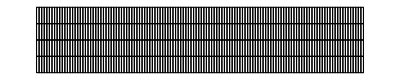

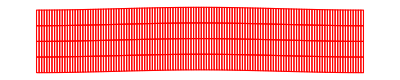

-Graphics-

```mathematica
(*a opět vykreslíme*)
Show[BeamMesh["Wireframe"], ImageSize->Full]
Show[BeamMeshDeformed, ImageSize->Full]
Show[
BeamMesh["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[GrayLevel[0.9]],FaceForm[]]]],
ElementMeshDeformation[BeamMesh,{uif,vif}, "ScalingFactor"->10]["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]],
ImageSize->Full]
```